```mathematica
Clear["`*"]
```

Chapter 7 Homework Template

Problem 1: Consider a periodic signal,  , that has a period of  s. It is an odd function in t, and the coefficients, or amplitudes, of its Fourier series for the first 5 harmonics are      . Reconstruct  using Mathematica and plot it for the first 3 periods. Your plot should look something like mine:
-Graphics-

Hint: T = 0.25 so .  Only since terms  are non-zero.  Then

3 Sin[8 π t]+5 Sin[16 π t]+7 Sin[24 π t]+9 Sin[32 π t]+6 Sin[40 π t]

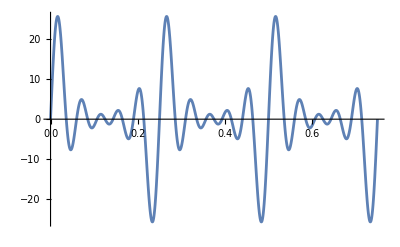

```mathematica
F[t_]=3*Sin[8*Pi*t]+5*Sin[8*Pi*t*2]+7*Sin[8*Pi*t*3]+9*Sin[8*Pi*t*4]+6*Sin[8*Pi*t*5]
Plot[F[t],{t,0,0.75}]
```

Problem 2 Find the average value of  by explicit integration over the interval x on 0 to  . The cleverest of you will use the Euler identities to modify the integrate to make it easily integrable.  After you do it the ‘hard way’ check your integration by using Mathematica to integrate the original form.

```mathematica
F[x_]=(Sin[x/2])^2
answer=Integrate[F[x],{x,0,Pi/2}]
answer/(Pi/2)
```

Sin[x/2]^2

1/4 (-2+π)

(-2+π)/(2 π)

Problem 3 Find the Fourier series for  on the interval  .  Do this the ‘hard way’ by first making a Mathematica function for , then make a function that evaluates the nth coefficients,  and . Then make a third function that explicitly adds up the Fourier cosine and sine series for an arbitrary number of harmonics N.  You will need to separately find the first term in the cosine series, . The make a plot of the original function, and its Fourier series for the first 10 terms to compare. 

Your plot should look like this: 
-Graphics-
Hint: If you think about this a bit, you might convince yourself that all the ’s are zero except .

3.14159+2 Sin[x]-Sin[2 x]+2/3 Sin[3 x]-1/2 Sin[4 x]+2/5 Sin[5 x]-1/3 Sin[6 x]+2/7 Sin[7 x]-1/4 Sin[8 x]+2/9 Sin[9 x]-1/5 Sin[10 x]

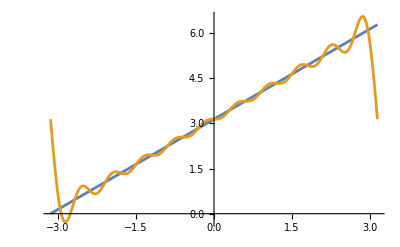

```mathematica
f4[x_]=Pi+x;
insideintB[x_,n_]=Sin[n*x]*f4[x];
coefficientB[x_,n_]=(1/Pi)*Integrate[insideintB[x,n],{x,-Pi,Pi}];
termB[x_,n_]=Sin[x*n]*coefficientB[x,n];
Fourierf4[x_]=(0.5/Pi)*(Integrate[f4[x],{x,-Pi,Pi}])+Sum[termB[x,n],{n,1,10}]
FourierSeries[f4[x],x,10];
Plot[{f4[x],Fourierf4[x]},{x,-Pi,Pi}]
```

Problem 4
Prove by direct calculation that   by using the Euler identities to rewrite the integrand into something you can integrate by hand. Don’t use Mathematica here. Instead, so me the algebra to do the conversion. One you have have converted the integrand, you can use -whatever- to do the integration. (Hint: We did this already in class - and in Homework 0)







Plugging in -L/2 also gives 0, meaning

Problem 5 Consider the function , but consider it on two different intervals, first from  to  and then a second time from 0 to . Find the Fourier Series for each of these two cases. They will be different. Tell me why they are different. (You’ll see it gives you the SAME function in the end! Either way! Let me start you out by showing you explicitly that functions are nominally “different” over the two intervals:

```mathematica
(* Let f5a be on the first interval and f5b be on the second*)
(* Look how I define the function on the second interval with the if statement! *)
f5a[x_] = x^2;
f5b[x_] = If[x<Pi,x^2,(x-2Pi)^2]; 
(*plot what this looks like*)
plot1 = Plot[f5a[x],{x,-Pi,Pi}]
plot2 = Plot[f5b[x],{x,0,2Pi}]
```

-Graphics-

-Graphics-

Now construct the Fourier series the “hard way” by making functions that explicitly find the ’s and ’s for BOTH cases, and then make functions that explicitly add up the Fourier series component for an arbitrary number of harmonics, N. Then plot the function and it’s series for the first 15 terms. Your  reproduction graphs should BOTH look like this:  
-Graphics-

See! It gives the SAME function over the interval.

10.3354-4 π Cos[x]+π Cos[2 x]-4/9 π Cos[3 x]+1/4 π Cos[4 x]-4/25 π Cos[5 x]+1/9 π Cos[6 x]-4/49 π Cos[7 x]+1/16 π Cos[8 x]-4/81 π Cos[9 x]+1/25 π Cos[10 x]-4/121 π Cos[11 x]+1/36 π Cos[12 x]-4/169 π Cos[13 x]+1/49 π Cos[14 x]-4/225 π Cos[15 x]

10.3354-4 π Cos[x]+π Cos[2 x]-4/9 π Cos[3 x]+1/4 π Cos[4 x]-4/25 π Cos[5 x]+1/9 π Cos[6 x]-4/49 π Cos[7 x]+1/16 π Cos[8 x]-4/81 π Cos[9 x]+1/25 π Cos[10 x]-4/121 π Cos[11 x]+1/36 π Cos[12 x]-4/169 π Cos[13 x]+1/49 π Cos[14 x]-4/225 π Cos[15 x]

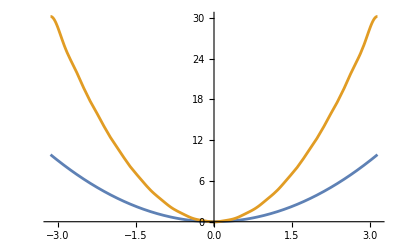
$DisplayFunction[-Graphics-]

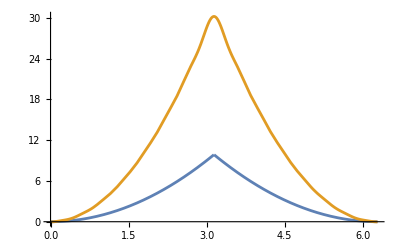
$DisplayFunction[-Graphics-]

```mathematica
Clear["`*"]
F1[x_]=x^2;
An1[x_,n_]=Integrate[F1[x]*Cos[n*x],{x,-Pi,Pi}];
Bn1[x_,n_]=Integrate[F1[x]*Sin[n*x],{x,-Pi,Pi}];
fourier1[x_]=(0.5*Integrate[F1[x],{x,-Pi,Pi}])+Sum[An1[x,n]*Cos[x*n],{n,1,15}]+Sum[Bn1[x,n]*Sin[x*n],{n,1,15}]
F2[x_]=If[x<Pi,x^2,(x-2Pi)^2];
An2[x_,n_]=Integrate[F2[x]*Cos[n*x],{x,0,2*Pi}];
Bn2[x_,n_]=Integrate[F2[x]*Sin[n*x],{x,0,2*Pi}];
fourier2[x_]=(0.5*Integrate[F2[x],{x,-Pi,Pi}])+Sum[An2[x,n]*Cos[x*n],{n,1,15}]+Sum[Bn2[x,n]*Sin[x*n],{n,1,15}]
Plot[{F1[x],fourier1[x]},{x,-Pi,Pi}]
Plot[{F2[x],fourier2[x]},{x,0,2*Pi}]
```

Problem 6 Consider the piecewise continuous function, f(x), such that  on the interval  and  on the interval  . 

Write a generic formula for the Fourier coefficients, or amplitudes,  and  for the nth terms in the series. Then use Mathematica to plot the function and it’s Fourier reproduction for the first 15 terms. I’ll start you out by showing how to write the function for the piecewise function. You will need to add the rest.

If[x<L/2,(2 h x)/L,2 h-(2 h x)/L]

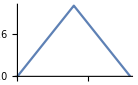

```mathematica
f6[x_,h_,L_] = If[x<L/2,2h x/L, 2h-(2h x/L)]
Plot[f6[x,1,4],{x,0,4}]
```

For simplicity, when you make function evaluations, let h = 1 and L = 4. 
See: the function’s Fourier Series is pretty straight forward: Your figure should look like this:
-Graphics-
Remember that it could be that either the ’s or ’s are all zero. You should be able to figure this out from the symmetry of the function!

If[x<2,x/2,2-x/2]

If[x<2,fourierpart1[x],fourierpart2[x]]

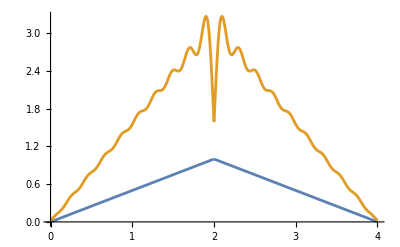
$DisplayFunction[-Graphics-]

```mathematica
Clear["`*"]
F1[x_]=If[x<2,x/2,2-x/2]
An1[x_,n_]=Integrate[x/2*Cos[n*x],{x,0,2}];
An2[x_,n_]=Integrate[(2-x/2)*Cos[n*x],{x,2,4}];
Bn1[x_,n_]=Integrate[x/2*Sin[n*x],{x,0,2}];
Bn2[x_,n_]=Integrate[(2-x/2)*Sin[n*x],{x,2,4}];
fourierpart1[x_]=0.5*Integrate[x/2,{x,0,2}]+Sum[An1[x,n]*Cos[n*x],{n,1,30}]+Sum[Bn1[x,n]*Sin[n*x],{n,1,30}];
fourierpart2[x_]=0.5*Integrate[(2-x/2),{x,2,4}]+Sum[An2[x,n]*Cos[n*x],{n,1,30}]+Sum[Bn2[x,n]*Sin[n*x],{n,1,30}];
fourierTotal[x_]=If[x<2,fourierpart1[x],fourierpart2[x]]
Plot[{F1[x],fourierTotal[x]},{x,0,4}]
```

Problem 7:  Consider the non-periodic function  defined as  on the interval  and  on the interval   and  everywhere else.  Write down the correct integrals (in LATEX, of course) for taking the Fourier Transform of this function (there two separate integrals), then use Mathematica to create the Fourier Transform of f(x) as the function F(k). (F(k) evaluates the integrals for an arbitrary value of k. You don’t need to specify k, Mathematica knows how to do the math!) Then plot the Fourier Transform as a function of k.

Your plot should look like this: 
-Graphics-
Can you see that this is sort of like the intensity function of single slit diffraction?  YOU SHOULD. It is very very similar to it. The diffraction pattern you see from slits IS THE FOURIER TRANSFORM of the slit function!

Piecewise[{{2+2 x, -1≤x≤0}, {2-2 x, 0<x≤1}, {0, True}}]

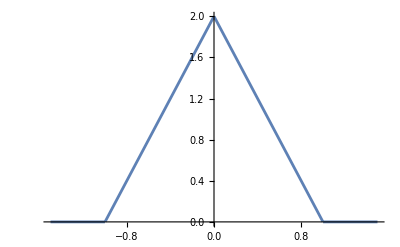

-Graphics-

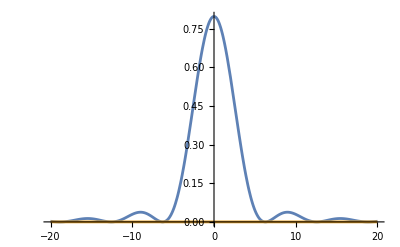

```mathematica
Clear["`*"]
ogfunction[x_]=Piecewise[{{2+2x,-1<=x<=0},{2-2x,0<x<=1}}]
Plot[ogfunction[x],{x,-1.5,1.5}]
g1[x_,n_]=(2a+2x)*Exp[-I*x*n];
g2[x_,n_]=(2a-2x)*Exp[-I*x*n];
f1[x_,n_]=Integrate[g1[x,n],{x,-a,0}]*(1/(2*Pi))*Exp[I*x*n];
f2[x_,n_]=Integrate[g2[x,n],{x,0,a}]*(1/(2*Pi))*Exp[I*x*n];
fourierpart1[x_]=Integrate[f1[x,n],{n,-a,0}];
fourierpart2[x_]=Integrate[f2[x,n],{n,0,a}];
fulltransform[x_,a_]=fourierpart1[x]+fourierpart2[x];
actualtransform[k_]=FourierTransform[ogfunction[x],x,k];
Plot[{Re[fulltransform[x,1]],Im[fulltransform[x,1]]},{x,-20,20},PlotRange->Full]
Plot[{Re[actualtransform[k]],Im[actualtransform[k]]},{k,-20,20},PlotRange->Full]
```

Problem 8:  Hmm... Please go through this and reconstruct it. For some reason in the whole history of this course, no one student has ever been able to reproduce this problem correctly even though every semester I hand out the exact notes showing how to do the problem and even though I DO the problem in class before its very eyes! ... So what is this? Voodoo Math? I don’t know.  But here goes:

Find the Fourier transform of the function , which is a standard Gaussian function centered on x = 0, with a standard deviation of . Wiki “Gaussian” if you need to understand what a standard deviation is, or what a Gaussian is.  In thus taking the Fourier transform, so that the “Fourier transform of a Gaussian” is also a Gaussian of the form . You’ll need to identify  after doing the integration. 

Here’s what was already given to you in the notes: This is a VERY VERY VERY IMPORTANT EXAMPLE:
It is deeply related to the “uncertainty principle” and is sort of at the root of Quantum Mechanical 
thinking!  This is the “gaussian wave packet”

NOTE  again the replacement of  “” in exponent with   here.  You can back substitute if you want. In general you can  ‘offset’ the gaussian by letting , which centers it a position .  For this specific problem 

So in general    ... its the  that makes is “gaussian”
It’s Fourier transform is 
  ... which wiggles, but is also a gaussian in 

where  is where the peak is centered and  is the ‘width’ of the peak.  

The transform, gausk(k) comes from
  (which is a mess to do by hand) 

The lesson here is that the “Fourier Transform of a Gaussian is also a Gaussian”, and that the “width of the peak in x-space goes like , but the width of the peak is “wave-space” or “momentum-space”, or “k-space”,  goes like .  The uncertainty “” is proportional to  and the uncertainly in momentum-space “” is proportional to . Thus .  The “Gaussian wave function” is the function with the minimum uncertainty.  You’ll learn much more of this in Modern Physics and QM. 

To do the problem by hand is a mess and I have given you the notes with the derivation, which involves “Completing the square” in the integral of the transform. But of course, with Mathematica you can  just ‘do it’. But  I would PLEASE PRETTY PLEASE, ask you to review the notes available to you on Canvas and carefully follow step by step the hand algebra and calculus of how to do the integration. 

First, Let’s just look at the Gaussian itself  to remind ourselves what it looks like.

```mathematica
Clear[σ,xo]
gausx[x_,σ_,xo_]=E^(-(x-xo)^2/(2 σ^2))
(* σ = 1;  Keep it all symbolic for now *)
(* Integrate it so see the "normalization" of a gaussian *)
Integrate[gausx[x,σ,xo],{x,-Infinity,Infinity}]

ⅇ^(-(x-xo)^2/(2 σ^2))
ConditionalExpression[(√(2 π))/(√(1/σ^2)), Re[σ^2]≥0]
```

```mathematica
(* here is a plot of the gaussian as function of x, with sigma and xo fixed *)

Plot[gausx[x,1,1],{x,-5,5}]
-Graphics-
```

OK, then  let’s let Mathematica  do the Fourier Transform the EASY way!

```mathematica
gausk[k_,σ_,xo_]=FourierTransform[gausx[x,σ,xo],x,k]
(ⅇ^(ⅈ k xo-(k^2 σ^2)/2))/(√(1/σ^2))
```

You can see above that the “gaussian” part is the  part.  NO FUSS, NO MUSS!
Let’s plot the spatial gaussian: gausx and the wave-space gaussian, gausk for both the real and imaginary parts, remembering that the Fourier Transform, in general has both a real and imaginary part!

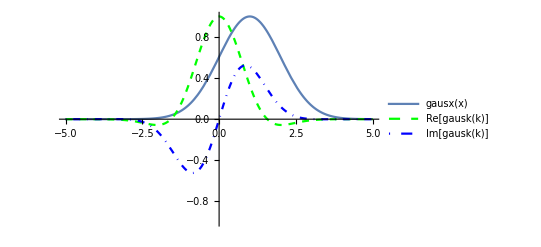
```mathematica
plot1 = Plot[gausx[x,1,1],{x,-5,5},PlotLegends->{"gausx(x)"},PlotRange->{-1,1}];
plot2 = Plot[Re[gausk[k,1,1]],{k,-5,5},PlotStyle -> {Dashed, Green},PlotLegends->{"Re[gausk(k)]"}];
plot3 = Plot[Im[gausk[k,1,1]],{k,-5,5},PlotStyle -> {DotDashed,Blue},PlotLegends->{"Im[gausk(k)]"}];
Show[plot1,plot2,plot3]


-Graphics-
```

Now Let’s Do it again, but for a different value of \sigma. Let’s make the space gaussian narrower by taking \sigma =1/4. This will make a much BROADER gaussian in wave-space for gausk.

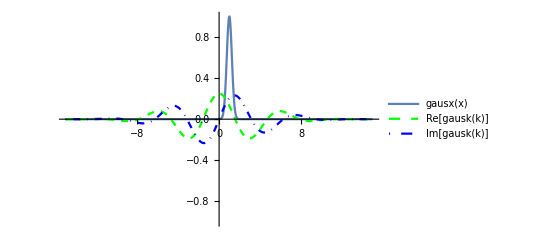
```mathematica
plot4 = Plot[gausx[x,0.25,1],{x,-15,15},PlotLegends->{"gausx(x)"},PlotRange->{-1,1}];
plot5 = Plot[Re[gausk[k,0.25,1]],{k,-15,15},PlotStyle -> {Dashed, Green},PlotLegends->{"Re[gausk(k)]"}];
plot6 = Plot[Im[gausk[k,0.25,1]],{k,-15,15},PlotStyle -> {DotDashed,Blue},PlotLegends->{"Im[gausk(k)]"}];
Show[plot4,plot5,plot6]
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{\"-\", \"2047.8431115761794`\"}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."
-Graphics-
```

So let’s do the “HARD” example of showing that the Fourier Transform of a Gaussian is also a Gaussian by completing the square. This what you SHOULD be able to do on a TEST BY HAND... OK? Will you follow this closely enough to do that. 

The form of a Gaussian is the so-called “Bell Curve”

where  is the half-width of the curve, and  is where the curve is centered. For the ease of calculation, I’m now going to take . We will now show that the Fourier transform of this is 


To do the integral, we need to “complete the square”.   Let    then the exponent of the integrand can be written as



(I’ve completed the square by taking the coefficient of ”b”, and writing is so that   can be factored as . 

Factoring out the constant term with  now gives: 


The final step is to let  and . That makes the integral be 

 so the final transform is:

   Compare to :      See the similarities? 

The difference is in the placement of .    is the “standard deviation” or “half-width” of the curve.  In f(x), the smaller  becomes, the narrower the peak, but in F(k), it is the opposite. The smaller  is, the BROADER the peak becomes.  This is the origin of the uncertainty principle. We will not do the calculation here, but the “uncertainty” is proportional to the width of the curve.  .  The product,  here. But in Quantum Mechanics,  is the uncertainty in momentum and  is the uncertainty in position. The product of these for ANY OTHER function set is greater than the minimum value given by gaussian wave states.

Problem 9 
Find the Fourier Transform of , namely , where  EVERYWHERE IN THE UNIVERSE EXCEPT on the interval  , were .  Then plot  and  over some suitable range and comment on what you learn from the shapes of these two functions.  (Write the correct  integral formulas for F(k) in LATEX, then use Mathematica to make a function to do the integral like you did in problem 7.)

If[-π/2≤x≤π/2,Cos[x],0]

Cos[(π x)/2]/(π (1-x^2))

(ⅇ^(ⅈ n x) Cos[(π x)/2])/(π (1-x^2))

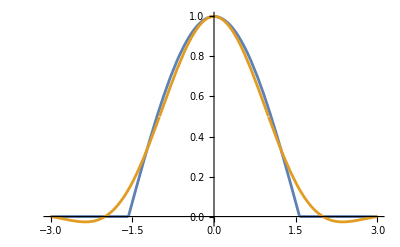

```mathematica
Clear["`*"]
F[x_]=If[(-Pi/2)<=x<=(Pi/2),Cos[x],0]
F2[x_]=(1/Pi)*(Cos[Pi*x/2]/(1-x^2))
G[x_,n_]=(1/2*Pi)*Integrate[Cos[x]*Exp[-I*n*x],{x,(-Pi/2),(Pi/2)}];
G2[x_,n_]= F2[x]*Exp[I*n*x]
fourier2[x_]=Integrate[G2[x,n],{n,-Pi/2,Pi/2}];
Plot[{F[x],fourier2[x]},{x,-3,3}]
```